## We check summation by parts for the Hierarchical basis in 1D

### Standard Definitions

```mathematica
ϕ[x_]:=If[Abs[x]>1,0,1-Abs[x]]
ϕ[l_,i_]:=If[l==-1,#,If[l==0,1-#,(ϕ[2^l(#-2^-l(2i-1))])]]&
ceil[x_]:=1+Floor[x]
dϕ[x_]:=If[Abs[x]>1,0,
			If[x==1 ,-1/2,
			If[x==-1,1/2,
			If[x==0,0,
			If[x>0,-1,1]]]]](* Don't think I need this*)

switch[x_]:=If[x≥1,x,1]

test[x_]:=Sin[Pi x]^2
dtest[x_]:=2 Pi Cos[Pi x] Sin[Pi x]
```

### Full Hierarchical Basis

```mathematica
getCoefficient[f_,x_,l_]:=f[x]-1/2 f[x+2^-l]-1/2 f[x-2^-l]
fullCoefficients[f_,l_]:={{f[1],f[0]}}~Append~Table[Table[getCoefficient[f,2^-k i,k],{i,1,2^k-1,2}],{k,1,l}]

Reconstruct[coefficients_]:=If[#==1,coefficients[[1,1]],
coefficients[[1,1]]#+coefficients[[1,2]](1-#)+Sum[coefficients[[2,l,ceil[2^(l-1)#]]] ϕ[2^l(#-2^-l(2ceil[2^(l-1)#]-1))],{l,1,Length[coefficients[[2]]]}]]&

project[f_,l_]:=Reconstruct[fullCoefficients[f,l]]
```

### Differentiation

```mathematica
diff[f_,l_]:=If[#< 2^-l, diff[diff[f,l+1],l+1][2^-l]# (*(f[#+2^(-l-2)]-f[#])/2^(-l-2)*),If[#> 1-2^-l, diff[diff[f,l+1],l+1][1-2^-l](#-1),(f[#+2^-l]-f[#-2^-l])/(2 2^-l)]]&
diffNaive[f_,l_]:=If[#< 2^-l,(f[#+2^-l]-f[#])/2^-l,If[#> 1-2^-l,(f[#]-f[#-2^-l])/2^-l ,(f[#+2^-l]-f[#-2^-l])/(2 2^-l)]]&
diffFree[f_,l_]:=(f[#+2^-l]-f[#-2^-l])/(2 2^-l)&
```

### The Algorithm:

```mathematica
matrix[n_]:=PadRight[Flatten[Table[Table[fullCoefficients[diffFree[ϕ[l,i],n],n]//Flatten,{i,1,2^(switch[l]-1)}],{l,-1,n}],1],Automatic,0]
```

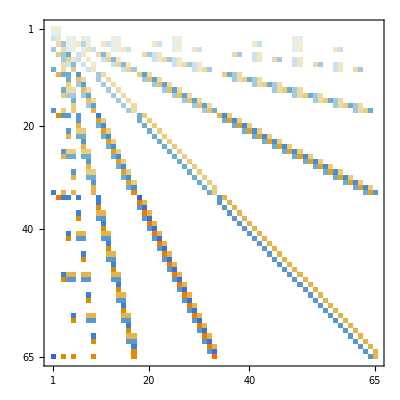

```mathematica
matrix[6]//MatrixPlot
```

```mathematica
fullW[n_]:=Flatten[Table[Table[Table[Table[NIntegrate[ϕ[l1,i1][x]ϕ[l2,i2][x],{x,0,1}],{i2,1,2^(switch[l2]-1)}],{l2,-1,n}]//Flatten,{i1,1,2^(switch[l1]-1)}],{l1,-1,n}],1]
```

```mathematica
fullW[4]//Dimensions
matrix[4]//Dimensions
```

{17,17}

{17,17}

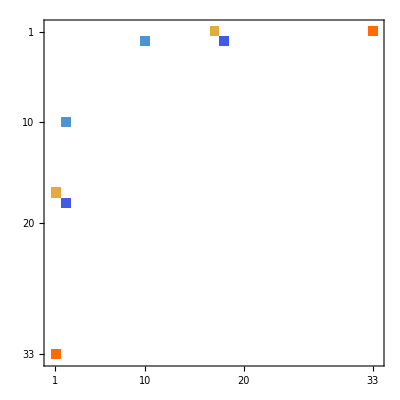

```mathematica
(*ArrayPlot[Table[Tooltip[#[[i,j]]],{i,1,17},{j,1,17}]&SetAccuracy[(#+Transpose[#]-fulldW[4])&@(matrix[4].fullW[4]),4]]*)

SetAccuracy[(#+Transpose[#]-fulldW[5])&@(matrix[5].fullW[5]),1]//MatrixPlot
```

When we used diffFree, we get exactly what we want. Only the two boundary functions contribute.

```mathematica
fulldW[n_]:=Flatten[Table[Table[Table[Table[ϕ[l1,i1][1]ϕ[l2,i2][1]-ϕ[l1,i1][0]ϕ[l2,i2][0],{i2,1,2^(switch[l2]-1)}],{l2,-1,n}]//Flatten,{i1,1,2^(switch[l1]-1)}],{l1,-1,n}],1]
```

```mathematica
SetAccuracy[(#+Transpose[#]-fulldW[4])&@(matrix[4].fullW[4]),4]
```

{{0.,0.,0.033,0.001,0.064,0.003,0.,0.,0.128,0.005,0.,0.,0.,0.,0.,0.,0.255},{0.,0.,-0.033,-0.064,-0.001,-0.128,0.,0.,-0.003,-0.255,0.,0.,0.,0.,0.,0.,-0.005},{0.033,-0.033,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.001,-0.064,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.064,-0.001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.003,-0.128,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.128,-0.003,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.005,-0.255,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.255,-0.005,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}